# Load packages

```mathematica
SetDirectory[NotebookDirectory[]<>"../package/"];
Get["funcs_rxns_moms.m"]
Needs["diffTVR`"]
```

```mathematica
?diffTVR`*
```

# Import

## Import cache

```mathematica
nv=3;
nh=1;

volExp=14;
cdir=getCacheDirRaw[volExp];
dataDesc=importDataDesc[cdir<>"data_desc.txt"];
```

```mathematica
SetDirectory[NotebookDirectory[]];

noIP3Rs={100,500,600,700,800,900,1000,1500,2000,2500,3000,3500,4000,4500,5000};
(*noIP3Rs={800};*)
ip3s={
"ip3_0p100","ip3_0p200","ip3_0p300","ip3_0p400","ip3_0p500","ip3_0p600","ip3_0p700","ip3_0p800","ip3_0p900","ip3_1p000",
"ip3_1p100","ip3_1p200","ip3_1p300","ip3_1p400","ip3_1p500","ip3_1p600","ip3_1p700","ip3_1p800","ip3_1p900","ip3_2p000"
};

ip3Keys={};
Do[
AppendTo[ip3Keys,{noIP3R,ip3}];
,{ip3,ip3s}
,{noIP3R,noIP3Rs}];

params0=Association[];

Monitor[
Do[
ip3Key=ip3Keys[[i]];
{noIP3R,ip3}=ip3Key;

cdir=getCacheDirRaw[volExp,noIP3R];
pLFDL=Association[];
Do[
pLFDL[k]=Flatten[Import[cdir<>"params0/"<>ip3<>"/"<>k<>".txt","Table"]]
,{k,makeLF[nv,nh]}];

params0[ip3Key]=makePStructFromLFDL[nv,nh,pLFDL];
,{i,Length[ip3Keys]}];
,ProgressIndicator[i,{1,Length[ip3Keys]}]]
```

## Viz

```mathematica
pltEvery=20;
timesPlt=dataDesc["times"][[;;;;pltEvery]];
```

```mathematica
makeLF[nv,nh]
lfPlt=Select[makeLF[nv,nh],StringLength[#]<4||(StringTake[#,4]!="varh"&&StringTake[#,3]!="muh")&]
```

{wt11,wt12,wt13,sig2,varh11,b1,b2,b3,muh1}

{wt11,wt12,wt13,sig2,b1,b2,b3}

```mathematica
pltParamsAcrossIP3s[params0_,noIP3R_,k_,ip3s_]:=Module[
{r,ip3,ip3Key,xPlt,colors,rngs}
,
rngs=<|
"wt11"->{0,1.5},
"wt12"->{-0.005,0.005},
"wt13"->{-1,1},
"sig2"->{0,0.00015},
"b1"->{-1.2,2.5},
"b2"->{-2,4},
"b3"->{-1.2,1.2}
|>;

colors=Table[ColorData["BrownCyanTones"][i/Length[ip3s]],{i,Length[ip3s]}];

r=Show[
Table[
ip3=ip3s[[i]];
ip3Key={noIP3R,ip3};
xPlt=params0[ip3Key]["LFDL"][k][[;;;;pltEvery]];
ListLinePlot[Transpose[{timesPlt,xPlt}],PlotRange->All,PlotLabel->k,PlotStyle->colors[[i]]]
,{i,Length[ip3s]}],
PlotRange->rngs[k],
PlotLabel->labels[k]<>" # IP3R: "<>ToString[noIP3R],
FrameLabel->{"Time (s)"}
];
Return[r];
];
```

```mathematica
(*
plts=Table[
Table[
pltParamsAcrossIP3s[params0,noIP3R,k,ip3s]
,{noIP3R,noIP3Rs}]
,{k,lfPlt}];

Grid[plts]
*)
```

```mathematica
pltParamsAcrossNoIP3Rs[params0_,ip3_,k_,noIP3Rs_]:=Module[
{r,noIP3R,ip3Key,xPlt,colors}
,
colors=Table[ColorData["BrownCyanTones"][i/Length[noIP3Rs]],{i,Length[noIP3Rs]}];

r=Show[
Table[
noIP3R=noIP3Rs[[i]];
ip3Key={noIP3R,ip3};
xPlt=params0[ip3Key]["LFDL"][k][[;;;;pltEvery]];
ListLinePlot[Transpose[{timesPlt,xPlt}],PlotRange->All,PlotLabel->k,PlotStyle->colors[[i]]]
,{i,Length[noIP3Rs]}],
PlotRange->All,
PlotLabel->ip3<>" "<>labels[k],
FrameLabel->{"Time (s)"}
];
Return[r];
];
```

```mathematica
(*
plts=Table[
pltParamsAcrossNoIP3Rs[params0,"ip3_0p500",k,noIP3Rs]
,{k,{"wt11","b1"}}];

colors=Table[ColorData["BrownCyanTones"][i/Length[noIP3Rs]],{i,Length[noIP3Rs]}];
leg=LineLegend[colors[[;;Length[noIP3Rs]]],noIP3Rs];

Grid[{Flatten[{leg,plts}]}]
*)
```

# Calculate derivs0

```mathematica
tvrDiff[nv_,nh_,lfNonConstant_,ip3Keys_,params_,dataDesc_,magZero_,alphas_]:=Module[
{dx,n,structsTVR,noOptSteps,derivs,ip3,dat,derivGuess,noIP3R,ip3Key,derivLFDL,iKey}
,
dx=1;
n=dataDesc["noTpts"];
structsTVR=makeTVRstructs[n,dx,0.0];
derivGuess=ConstantArray[0,n-1];

noOptSteps=10;
derivs=Association[];

Monitor[
Do[
ip3Key=ip3Keys[[iKey]];
{noIP3R,ip3}=ip3Key;

derivLFDL=Association[];
Do[

dat=params[ip3Key]["LFDL"][k];

If[MemberQ[lfNonConstant,k],

(* Differentiate *)
structsTVR["alpha"]=alphas[k];
derivLFDL[k]=getDiffTVRGivenStructs[dat,derivGuess,noOptSteps,structsTVR];

(* Set small magnitudes to zero *)
derivLFDL[k]=Table[If[Abs[x]<magZero,0.0,x],{x,derivLFDL[k]}];
,

(* Constant *)
derivLFDL[k]=ConstantArray[0.0,n-1];
];

,{k,makeLF[nv,nh]}];

derivs[ip3Key]=makePStructFromLFDL[nv,nh,derivLFDL];

,{iKey,Length[ip3Keys]}];
,ProgressIndicator[iKey,{1,Length[ip3Keys]}]];

Return[{derivs,structsTVR}];
]
```

```mathematica
makeFilteredFromDerivs[nv_,nh_,lfNonConstant_,lfConstantNonZero_,lfConstantZero_,ip3Keys_,derivs_,params_,structsTVR_,dataDesc_]:=Module[
{filtered,initPt,fLFDL,meanVal}
,
filtered=Association[];
Do[
fLFDL=Association[];

Do[
If[MemberQ[lfNonConstant,k],
initPt=params[ip3Key]["LFDL"][k][[1]];
fLFDL[k]=initPt+structsTVR["amat"].derivs[ip3Key]["LFDL"][k];
fLFDL[k]=Flatten[{initPt,fLFDL[k]}];
];

If[MemberQ[lfConstantNonZero,k],
meanVal=Mean[params[ip3Key]["LFDL"][k]];
fLFDL[k]=ConstantArray[meanVal,dataDesc["noTpts"]];
];

If[MemberQ[lfConstantZero,k],
fLFDL[k]=ConstantArray[0.0,dataDesc["noTpts"]];
];

,{k,makeLF[nv,nh]}];

filtered[ip3Key]=makePStructFromLFDL[nv,nh,fLFDL];
,{ip3Key,ip3Keys}];

Return[filtered]
]
```

```mathematica
makeLF[nv,nh]
```

{wt11,wt12,wt13,sig2,varh11,b1,b2,b3,muh1}

```mathematica
lfNonConstant={"wt11","b1"};
lfConstantZero={"wt13","muh1"};
lfConstantNonZero={"b3","varh11","wt12","b2","sig2"};
```

```mathematica
alphas=<|
"wt11"->100,
"b1"->100
|>;

(*
alphas=<|
"wt11"->250,
"b1"->25
|>;
*)
```

```mathematica
magZero=10^-5;
{derivs,structsTVR}=tvrDiff[nv,nh,lfNonConstant,ip3Keys,params0,dataDesc,magZero,alphas];
```

```mathematica
filtered=makeFilteredFromDerivs[nv,nh,lfNonConstant,lfConstantNonZero,lfConstantZero,ip3Keys,derivs,params0,structsTVR,dataDesc];
```

```mathematica
momentsFilteredTrue=Association[];
Do[
momentsFilteredTrueLD=Table[convertParamsToMoments[nv,x],{x,filtered[ip3Key]["LD"]}];
momentsFilteredTrue[ip3Key]=makeMStructFromLD[nv,nh,momentsFilteredTrueLD];
,{ip3Key,ip3Keys}];
```

```mathematica
momentsTrue=Association[];
Do[
momentsTrueLD=Table[convertParamsToMoments[nv,x],{x,params0[ip3Key]["LD"]}];
momentsTrue[ip3Key]=makeMStructFromLD[nv,nh,momentsTrueLD];
,{ip3Key,ip3Keys}];
```

```mathematica
pltEvery=20;
timesPlt=dataDesc["times"][[;;;;pltEvery]];
colors=Table[ColorData["BrownCyanTones"][i/Length[ip3s]],{i,Length[ip3s]}]
```

{RGBColor[0.4328202, 0.2875746, 0.16778140000000002],RGBColor[0.5179634, 0.3752862, 0.2504938],RGBColor[0.5943548, 0.45806840000000004, 0.33588],RGBColor[0.6619944, 0.5359212, 0.42394],RGBColor[0.729634, 0.613774, 0.512],RGBColor[0.7668376, 0.6736248, 0.5867076],RGBColor[0.8040412, 0.7334756, 0.6614152],RGBColor[0.8253242000000001, 0.787301, 0.7308212],RGBColor[0.8306866, 0.835101, 0.7949256],RGBColor[0.836049, 0.882901, 0.85903],RGBColor[0.8065450000000001, 0.9053942, 0.8961547999999999],RGBColor[0.777041, 0.9278874, 0.9332796],RGBColor[0.7376514, 0.9364448, 0.9557662],RGBColor[0.6883762, 0.9310664, 0.9636146],RGBColor[0.639101, 0.925688, 0.971463],RGBColor[0.585357, 0.8967528, 0.9580974],RGBColor[0.531613, 0.8678176000000001, 0.9447318],RGBColor[0.4723912, 0.8128028, 0.9049796],RGBColor[0.40769160000000004, 0.7317084, 0.8388408],RGBColor[0.342992, 0.650614, 0.772702]}

```mathematica
pltTVR[derivs_,noIP3R_,k_]:=Module[
{rngs,r,ip3,ip3Key,xPlt}
,
rngs=<|
"wt11"->{-0.002,0.01},
"b1"->{-0.03,0.05},
"b3"->{-1,1},
"b2"->{-2,2},
"wt12"->Automatic,
"sig2"->Automatic
|>;

r=Show[
Table[
ip3=ip3s[[i]];
ip3Key={noIP3R,ip3};
 xPlt=derivs[ip3Key]["LFDL"][k][[;;;;pltEvery]];
ListLinePlot[Transpose[{timesPlt[[;;-2]],xPlt}],PlotRange->All,PlotStyle->colors[[i]]]
,{i,Length[ip3s]}],
PlotRange->rngs[k],
PlotLabel->"TVR deriv: "<>labels[k]<>" "<>ToString[noIP3R],
FrameLabel->{"Time (s)"}
];
Return[r];
]
```

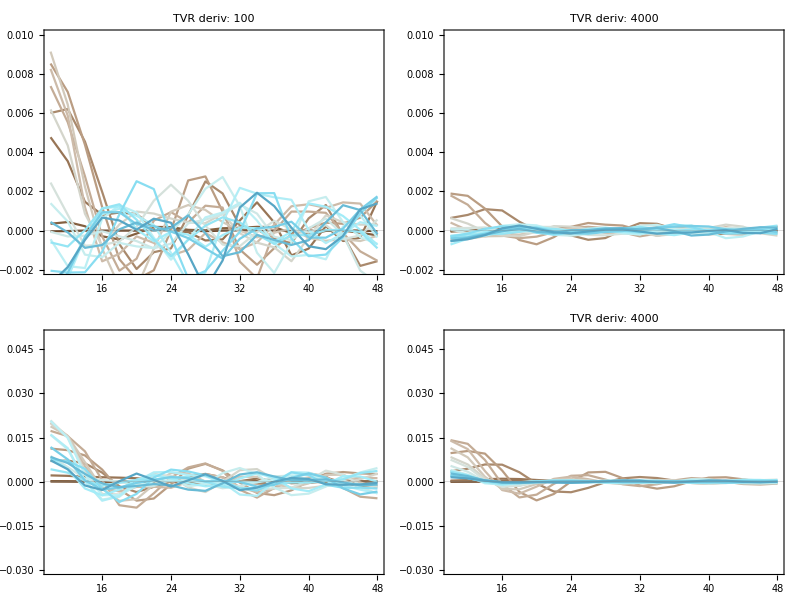

```mathematica
noIP3RsPlt=Select[{100,4000},MemberQ[noIP3Rs,#]&];
plts=Table[
Table[
pltTVR[derivs,noIP3R,k]
,{noIP3R,noIP3RsPlt}]
,{k,{"wt11","b1"}}];
p=Grid[plts]
```

```mathematica
pltFiltered[params0_,filtered_,noIP3R_,k_]:=Module[
{r,ip3,ip3Key,xPlt}
,
r=Show[
Table[
ip3=ip3s[[i]];
ip3Key={noIP3R,ip3};
xPlt=params0[ip3Key]["LFDL"][k][[;;;;pltEvery]];
ListLinePlot[Transpose[{timesPlt,xPlt}],PlotRange->All,PlotLabel->k,PlotStyle->LightGray]
,{i,Length[ip3s]}],
Table[
ip3=ip3s[[i]];
ip3Key={noIP3R,ip3};
xPlt=filtered[ip3Key]["LFDL"][k][[;;;;pltEvery]];
ListLinePlot[Transpose[{timesPlt,xPlt}],PlotRange->All,PlotLabel->k,PlotStyle->colors[[i]]]
,{i,Length[ip3s]}],
PlotRange->All,
PlotLabel->labels[k]<>" "<>ToString[noIP3R],
FrameLabel->{"Time (s)"}
];
Return[r]
]
```

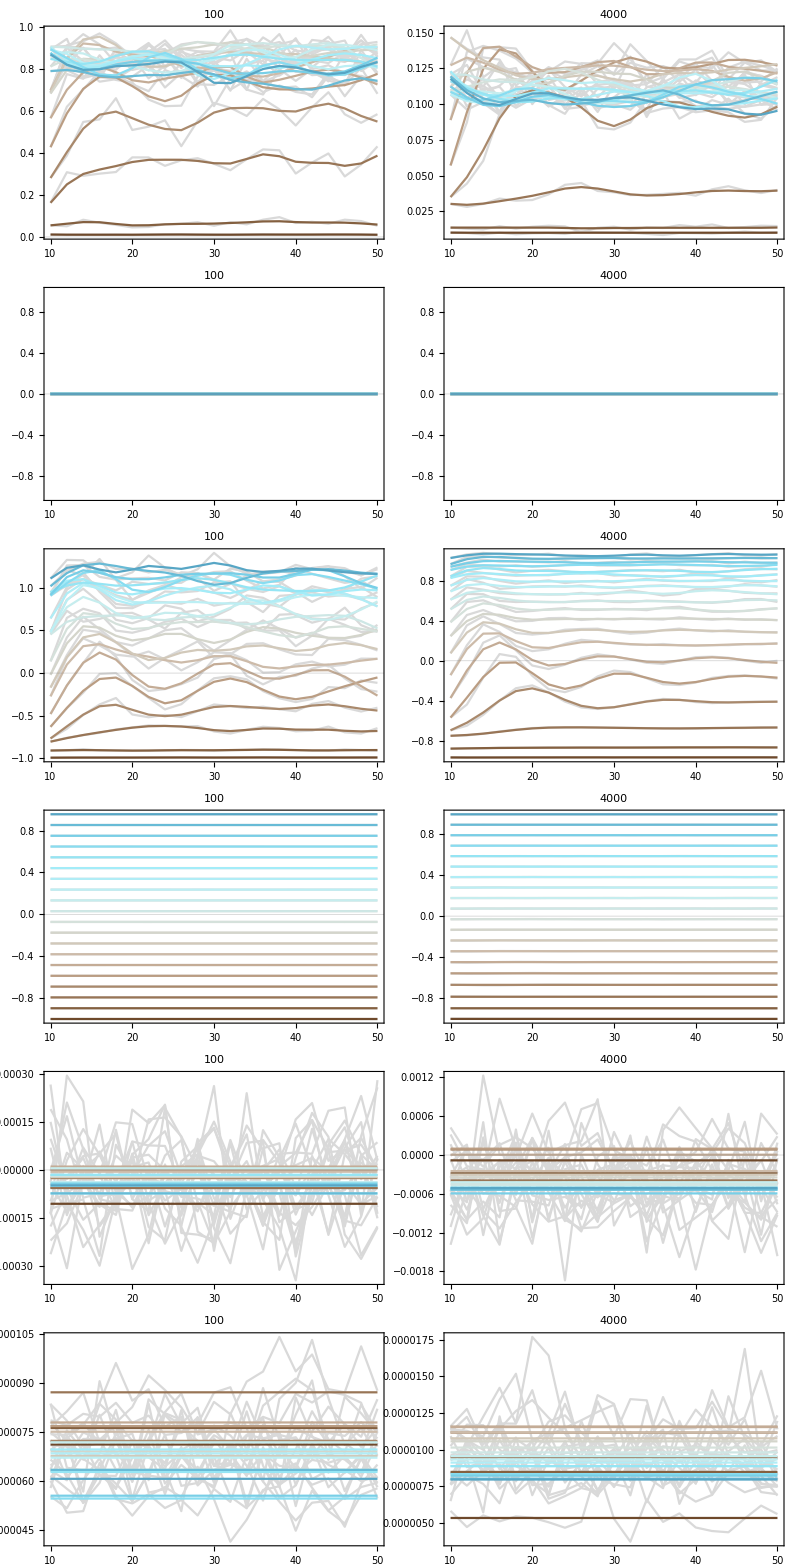

```mathematica
noIP3RsPlt=Select[{100,4000},MemberQ[noIP3Rs,#]&];
plts=Table[
Table[
pltFiltered[params0,filtered,noIP3R,k]
,{noIP3R,noIP3RsPlt}]
,{k,{"wt11","wt13","b1","b2","wt12","sig2"}}];
p=Grid[plts]
```

```mathematica
pltMoments[momentsTrue_,momentsFilteredTrue_,noIP3R_,k_]:=Module[
{r,ip3,ip3Key}
,
r=Show[
Table[
ip3=ip3s[[i]];
ip3Key={noIP3R,ip3};
xPlt=momentsTrue[ip3Key]["LFDL"][k][[;;;;pltEvery]];
ListLinePlot[Transpose[{timesPlt,xPlt}],PlotRange->All,PlotLabel->k,PlotStyle->LightGray]
,{i,Length[ip3s]}],
Table[
ip3=ip3s[[i]];
ip3Key={noIP3R,ip3};
xPlt=momentsFilteredTrue[ip3Key]["LFDL"][k][[;;;;pltEvery]];
ListLinePlot[Transpose[{timesPlt,xPlt}],PlotRange->All,PlotLabel->k,PlotStyle->colors[[i]]]
,{i,Length[ip3s]}],
PlotRange->All,
PlotLabel->ToString[noIP3R]<>" "<>k,
FrameLabel->{"Time (s)"}
];
Return[r]
]
```

```mathematica
makeLFM[nv,nh]
```

{mu1,mu2,mu3,mu4,var11,var12,var13,var14,var22,var23,var24,var33,var34,var44}

{100,4000}

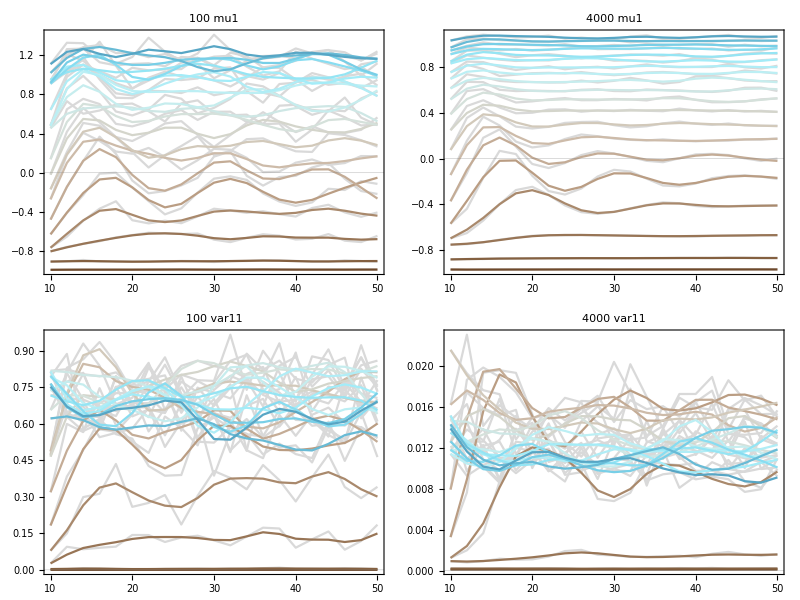

```mathematica
noIP3RsPlt=Select[{100,4000},MemberQ[noIP3Rs,#]&]

lfmPlt={"mu1","var11"};
plts=Table[
Table[
pltMoments[momentsTrue,momentsFilteredTrue,noIP3R,k]
,{noIP3R,noIP3RsPlt}]
,{k,lfmPlt}];
p=Grid[plts]
```

## Export

```mathematica
exportToCache[params_,dataDesc_,subdir_]:=Module[
{x,cdir,noIP3R,ip3,dir,ip3Key}
,
Do[
ip3Key=Keys[params][[i]];
{noIP3R,ip3}=ip3Key;

cdir=getCacheDir[dataDesc,noIP3R]<>subdir;
dir=cdir<>ip3;

If[!DirectoryQ[dir],CreateDirectory[dir]];
Do[
x=params[ip3Key]["LFDL"][k];
Export[dir<>"/"<>k<>".txt",StringRiffle[ToString[#,FortranForm]&/@PaddedForm[#,16]&/@x,"\n"]]
,{k,makeLF[nv,nh]}];

,{i,Length[Keys[params]]}];
]
```

```mathematica
noToStr[x_]:=StringReplace[ToString[PaddedForm[x,{3,1}]],{"."->"p","-"->"m"," "->""}]
```

```mathematica
subdir="derivs0/";
exportToCache[derivs,dataDesc,subdir];

subdir="filtered0/";
exportToCache[filtered,dataDesc,subdir];
```